```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\El Babbel\Desktop\Studium\GP2

```mathematica
Needs["ErrorBarPlots`"]
```

(*Aufgabe 1 a*)

```mathematica
LinReg[daten_]:=Module[{x,y,Δy,s,Δa0,Δb0,a0,b0,n, mittelY, RQ, sq},
n = Length[daten];
x = daten[[All,1]];
y = daten[[All,2]];
Δy = daten[[All,3]];
mittelY = (∑_(i=1)^n y[[i]]/Δy[[i]]^2)/(∑_(i=1)^n 1/Δy[[i]]^2);s = ∑_(i=1)^n 1 / (Δy[[i]])^2 *∑_(i=1)^n (x[[i]])^2 / (Δy[[i]])^2 - (∑_(i=1)^n x[[i]] / (Δy[[i]])^2 )^2;
a0 = 1/s *(∑_(i=1)^n (x[[i]])^2 / (Δy[[i]])^2  * ∑_(i=1)^n y[[i]]/ (Δy[[i]])^2  - ∑_(i=1)^n x[[i]] / (Δy[[i]])^2  *∑_(i=1)^n (x[[i]] * y[[i]]) / (Δy[[i]])^2);
b0 = 1/s *(∑_(i=1)^n 1/ (Δy[[i]])^2  * ∑_(i=1)^n (x[[i]] * y[[i]])/ (Δy[[i]])^2  - ∑_(i=1)^n x[[i]] / (Δy[[i]])^2  *∑_(i=1)^n y[[i]] / (Δy[[i]])^2);
Δa0 = Sqrt[1 / s *(∑_(i=1)^n x[[i]]^2/(Δy[[i]])^2)];
Δb0 = Sqrt[1 / s * (∑_(i=1)^n 1 / (Δy[[i]])^2)];
RQ = 1- (∑_(i=1)^n (y[[i]] - a0- b0 x[[i]])^2/Δy[[i]]^2)/(∑_(i=1)^n (y[[i]]-mittelY)^2/Δy[[i]]^2);
sq = 1/(n-2) *(∑_(i=1)^n ((y[[i]]-a0-b0 x[[i]])/Δy[[i]])^2);
Print["Berechnung der Fehler aus den Eingangsfehlern"];
Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"Bestimmtheitsmaß",RQ,""}, {"SQudrat",sq,""}} ]];
{b -> b0,Δb -> Δb0,a -> a0,Δa-> Δa0, sQudrat -> sq, RQuadrat -> RQ, Anzahl -> n}
]

linear =  ReadList["linear.txt",{Real,Real,Real}]
```

{{0.,2.8,1.},{2.,5.2,1.5},{4.,6.8,1.2},{6.,9.6,0.9},{8.,11.2,1.4},{10.,14.,1.4},{12.,15.6,1.5},{14.,17.,1.2},{16.,19.8,1.3},{18.,21.4,1.5}}

(*Augabe 1 b*)

```mathematica
regerg =LinReg[linear]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | 1.03634 | 0.0685982
Achsenabschnitt a | 3.01566 | 0.675303
Bestimmtheitsmaß | 0.996646 | 
SQudrat | 0.0960202 |

{b→1.03634,Δb→0.0685982,a→3.01566,Δa→0.675303,sQudrat→0.0960202,RQuadrat→0.996646,Anzahl→10}

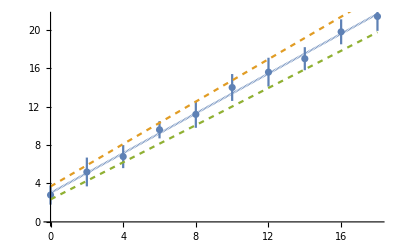

```mathematica
Show[ErrorListPlot[linear],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.regerg],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```

```mathematica
exponential = ReadList["exp.txt",{Real,Real,Real}]
```

{{0.,82.,1.},{2.,56.,1.},{4.,37.,1.},{6.,26.,1.},{8.,18.,1.},{10.,11.,1.},{12.,9.,1.},{14.,5.,1.},{16.,3.,1.}}

```mathematica
linearisiert = Replace[exponential,{xi_,yi_,Δyi_}->{xi,Log[yi], Δyi/ yi},2]
```

{{0.,4.40672,0.0121951},{2.,4.02535,0.0178571},{4.,3.61092,0.027027},{6.,3.2581,0.0384615},{8.,2.89037,0.0555556},{10.,2.3979,0.0909091},{12.,2.19722,0.111111},{14.,1.60944,0.2},{16.,1.09861,0.333333}}

```mathematica
linsierterg = LinReg[linearisiert]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | -0.193466 | 0.00365475
Achsenabschnitt a | 4.40686 | 0.010881
Bestimmtheitsmaß | 0.998766 | 
SQudrat | 0.4946 |

{b→-0.193466,Δb→0.00365475,a→4.40686,Δa→0.010881,sQudrat→0.4946,RQuadrat→0.998766,Anzahl→9}

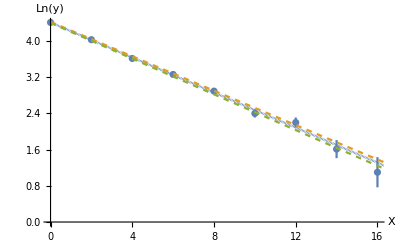

```mathematica
Show[ErrorListPlot[linearisiert,AxesLabel->{"X","Ln(y)"}],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.linsierterg],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```

(*Aufgabe 2*)

```mathematica
experg = LinReg[exponential]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | -4.5 | 0.0645497
Achsenabschnitt a | 63.4444 | 0.614636
Bestimmtheitsmaß | 0.854698 | 
SQudrat | 118.032 |

{b→-4.5,Δb→0.0645497,a→63.4444,Δa→0.614636,sQudrat→118.032,RQuadrat→0.854698,Anzahl→9}

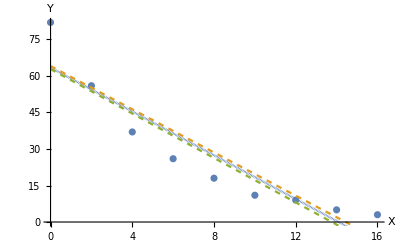

```mathematica
Show[ErrorListPlot[exponential,AxesLabel->{"X","Y"}],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.experg],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```

Die Grenzgeraden beinhalten nur 2 von 9 Punkten, ich hätte, wenn ich dass als linear annehmen müsste die Grenzgeraden weiter auseinander gezeichnet. Das sie so eng beieinander liegen, liegt an den vergleichsweise kleinen Fehlern. Man erkennt aber mit der Größe X^2/(n-2) gut erkennen, dass das Modell nich stimmt, da der Wert viel zugroß ist.*)

(*Aufgabe 3 a*)

{{0.,2.8,4.},{2.,5.2,6.},{4.,6.8,4.8},{6.,9.6,3.6},{8.,11.2,5.6},{10.,14.,5.6},{12.,15.6,6.},{14.,17.,4.8},{16.,19.8,5.2},{18.,21.4,6.}}

```mathematica
linear4=Replace[linear,{xi_,yi_,Δyi_}->{xi,yi,4*Δyi},2]
```

{{0.,2.8,4.},{2.,5.2,6.},{4.,6.8,4.8},{6.,9.6,3.6},{8.,11.2,5.6},{10.,14.,5.6},{12.,15.6,6.},{14.,17.,4.8},{16.,19.8,5.2},{18.,21.4,6.}}

```mathematica
GewLinReg[daten_] := Module[{x,y,Δy,fi,S,sq,Δa0,Δb0,a0,b0,n, mittelY, RQ, sq2},
n = Length[daten];
x = daten[[All,1]];
y = daten[[All,2]];
Δy = daten[[All,3]];
fi = Δy /4;
mittelY = (∑_(i=1)^n y[[i]]/fi[[i]]^2)/(∑_(i=1)^n 1/fi[[i]]^2);S = ∑_(i=1)^n 1 / (fi[[i]])^2 *∑_(i=1)^n (x[[i]])^2 / (fi[[i]])^2 - (∑_(i=1)^n x[[i]] / (fi[[i]])^2 )^2;
a0 = 1/S *(∑_(i=1)^n (x[[i]])^2 / (fi[[i]])^2  * ∑_(i=1)^n y[[i]]/ (fi[[i]])^2  - ∑_(i=1)^n x[[i]] / (fi[[i]])^2  *∑_(i=1)^n (x[[i]] * y[[i]]) / (fi[[i]])^2);
b0 = 1/S*(∑_(i=1)^n 1/ (fi[[i]])^2  * ∑_(i=1)^n (x[[i]] * y[[i]])/ (fi[[i]])^2  - ∑_(i=1)^n x[[i]] / (fi[[i]])^2  *∑_(i=1)^n y[[i]] / (fi[[i]])^2);
sq = 1/(n-2) *(∑_(i=1)^n ((y[[i]]-a0-b0 x[[i]])/fi[[i]])^2);
Δa0 = Sqrt[sq / S *(∑_(i=1)^n x[[i]]^2/(fi[[i]])^2)];
Δb0 = Sqrt[sq / S * (∑_(i=1)^n 1 / (fi[[i]])^2)];
RQ = 1- (∑_(i=1)^n (y[[i]] - a0- b0 x[[i]])^2/fi[[i]]^2)/(∑_(i=1)^n (y[[i]]-mittelY)^2/fi[[i]]^2);
sq2 = 1/(n-2) *(∑_(i=1)^n ((y[[i]]-a0-b0 x[[i]])/Δy[[i]])^2);

Print["Berechnung der Fehler aus den Streuung"];
Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"Bestimmtheitsmaß",RQ,""}, {"sQuadrat",sq2,""}} ]];
{b -> b0,Δb -> Δb0,a -> a0,Δa-> Δa0, squadrat -> sq2, RQuadrat -> RQ, Anzahl -> n}
]
```

```mathematica
reggew = GewLinReg[linear]
```

Berechnung der Fehler aus den Streuung

| Wert | Fehler
Steigung b | 1.03634 | 0.0212566
Achsenabschnitt a | 3.01566 | 0.209257
Bestimmtheitsmaß | 0.996646 | 
sQuadrat | 0.0960202 |

{b→1.03634,Δb→0.0212566,a→3.01566,Δa→0.209257,squadrat→0.0960202,RQuadrat→0.996646,Anzahl→10}

```mathematica
reggew4 = GewLinReg[linear4]
```

Berechnung der Fehler aus den Streuung

| Wert | Fehler
Steigung b | 1.03634 | 0.0212566
Achsenabschnitt a | 3.01566 | 0.209257
Bestimmtheitsmaß | 0.996646 | 
sQuadrat | 0.00600126 |

{b→1.03634,Δb→0.0212566,a→3.01566,Δa→0.209257,squadrat→0.00600126,RQuadrat→0.996646,Anzahl→10}

```mathematica
reg4 = LinReg[linear4]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | 1.03634 | 0.274393
Achsenabschnitt a | 3.01566 | 2.70121
Bestimmtheitsmaß | 0.996646 | 
SQudrat | 0.00600126 |

{b→1.03634,Δb→0.274393,a→3.01566,Δa→2.70121,sQudrat→0.00600126,RQuadrat→0.996646,Anzahl→10}

```mathematica
reg = LinReg[linear]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | 1.03634 | 0.0685982
Achsenabschnitt a | 3.01566 | 0.675303
Bestimmtheitsmaß | 0.996646 | 
SQudrat | 0.0960202 |

{b→1.03634,Δb→0.0685982,a→3.01566,Δa→0.675303,sQudrat→0.0960202,RQuadrat→0.996646,Anzahl→10}

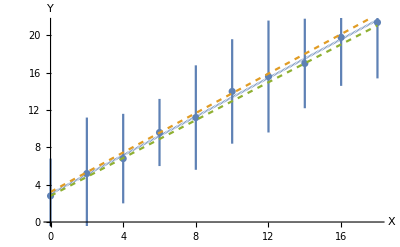

```mathematica
Show[ErrorListPlot[linear4,AxesLabel->{"X","Y"}],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.reggew4],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```

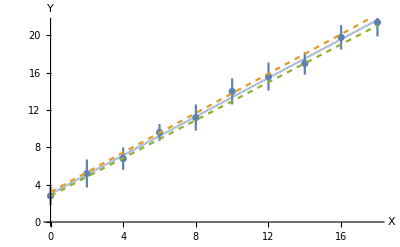

```mathematica
Show[ErrorListPlot[linear,AxesLabel->{"X","Y"}],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.reggew],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```

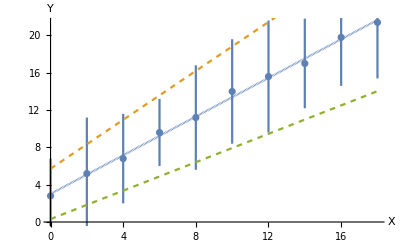

```mathematica
Show[ErrorListPlot[linear4,AxesLabel->{"X","Y"}],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.reg4],{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]
```

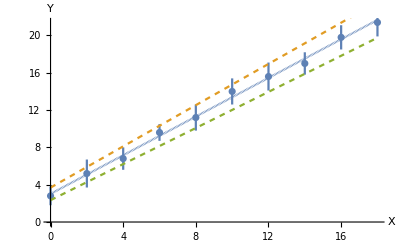

```mathematica
Show[ErrorListPlot[linear,AxesLabel->{"X","Y"}],Plot[Evaluate[{b t +a, (b + Δb) t + a + Δa,(b - Δb) t + a - Δa}/.reg,{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]]
```

Bei dem gewichetem Verfahren sind die Fehler der Parameter um einiges kleiner, daher sind die Grenzgeraden näher beieinander. Ansonsten ändert die Gewichtung der Streuung nichts. Mit dem Vervierfachen der Messfehler ist die Größe X^2/(n-2) um einiges kleiner geworden, aber sie variiert nicht mit dem Verfahren. R^2 ist bei allen 4 Funktionsaufrufen gleich, genau wie die Paramter a und b und die Anzahl der Messwerte sowieso.

Aufgabe 4

```mathematica
UrGerade[daten_] :=Module[{x,y,Δy,mittelY,RQ,sq,b0,Δb0,n,consto},
n = Length[daten];
x = daten[[All,1]];
y = daten[[All,2]];
Δy = daten[[All,3]];

consto = ∑_(i=1)^n (x[[i]]^2/Δy[[i]]^2);
b0= (∑_(i=1)^n (x[[i]]*y[[i]]/Δy[[i]]^2))/consto;
Δb0 = Sqrt[∑_(i=1)^n (x[[i]]/(Δy[[i]]*consto))^2];
sq = (1/(n-1)) *(∑_(i=1)^n ((y[[i]]-b0 x[[i]])/Δy[[i]])^2);
mittelY = (∑_(i=1)^n y[[i]]/Δy[[i]]^2)/(∑_(i=1)^n 1/Δy[[i]]^2);
RQ = 1- (∑_(i=1)^n (y[[i]] - b0 x[[i]])^2/Δy[[i]]^2)/(∑_(i=1)^n (y[[i]]-mittelY)^2/Δy[[i]]^2);
Print["Berechnung der Fehler aus den Eingangsfehlern"];
Print[TableForm[{{"","Wert","Fehler"},{"Steigung b",b0,Δb0},{"Achsenabschnitt a",a0,Δa0},{"Bestimmtheitsmaß",RQ,""}, {"sQuadrat",sq,""}} ]];
{b -> b0,Δb -> Δb0,a -> 0,Δa-> 0, squadrat -> sq, RQuadrat -> RQ, Anzahl -> n}]
```

```mathematica
urlin =UrGerade[linear]
```

Berechnung der Fehler aus den Eingangsfehlern

| Wert | Fehler
Steigung b | 1.28637 | 0.039634
Achsenabschnitt a | a0 | Δa0
Bestimmtheitsmaß | 0.909563 | 
sQuadrat | 2.30113 |

{b→1.28637,Δb→0.039634,a→0,Δa→0,squadrat→2.30113,RQuadrat→0.909563,Anzahl→10}

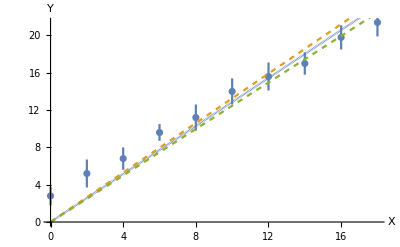

```mathematica
Show[ErrorListPlot[linear,AxesLabel->{"X","Y"}],Plot[Evaluate[{b t , (b + Δb) t ,(b - Δb) t }/.urlin,{t,0,18}, PlotStyle->{Dashing[{.0}],Dashing[{0.01}],Dashing[{0.01}]}]]]
```